# Code

```mathematica
importALPSGenes[filename_]:=Select[Import[filename,"Table"], Length[#] == geneCount&]
```

```mathematica
importALPSOut[filename_] := Select[Import[filename,"Table"], Length[#] == 3&]
```

```mathematica
importGenesFromRun[resultName_, expName_, runNo_] := Module[{file},
file= Last[FileNames[resultName <> "/" <> ToString[expName] <> "/" <> ToString[runNo] <> "-*.pop"]];
importALPSGenes[file]]
```

```mathematica
importResults[directoryName_] := Module[{files},
files = FileNames["*.out",{directoryName},2];
combineResults[Map[{FileBaseName[DirectoryName[#]] , importALPSOut[#]}&, files]]]
```

```mathematica
chartOfResults[directoryName_] := Module[{res},
res = importResults[directoryName];
BarChart[Map[Mean,values[res]], 
	ChartLegends -> keys[res], ChartStyle -> "DarkRainbow"]]
```

```mathematica
combineResultsHelper[splitResult_] := Module[{name, justData},
name = splitResult[[1,1]];
justData = Map[#[[2]]&, splitResult];
name ->  Map[#[[-1,-1]]&, justData]]
```

```mathematica
combineResults[results_] := Module[{},
Map[combineResultsHelper, SplitBy[results, #[[1]]&]]]
```

```mathematica
indexOfMinimum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Min[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
indexOfMaximum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Max[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
importMinGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMinimum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importBestGenes::notuniq]];
index = First[indexes];
genes[[index]]]
```

```mathematica
importMaxGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMaximum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importBestGenes::notuniq]];
index = First[indexes];
genes[[index]]]
```

# Read Results

```mathematica
target = {0, 0.1}
```

{0,0.1}

```mathematica
fitness = fitnessToTarget[#, target, Ao, 1]&;
fitnessData = fitnessToTargetData[#, target, Ao, 1]&;
```

```mathematica
fitness = fitnessToTarget[#, target, Ap, 1]&;
fitnessData = fitnessToTargetData[#, target, Ap, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Bp, 1]&;
fitnessData = fitnessForSpeedData[#, Bp, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Ap, 1]&;
fitnessData = fitnessForSpeedData[#, Ap, 1]&;
```

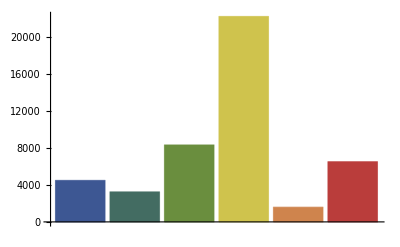
-Graphics--Graphics- | 0
-Graphics- | 1
-Graphics- | Ao
-Graphics- | Ap
-Graphics- | Bo
-Graphics- | Bp

```mathematica
chartOfResults["res1"]
```

```mathematica
target = {0,1} .4 m //. params
```

{0.,0.4}

```mathematica
RK4StepSize = 0.02;
```

```mathematica
target = {0,1} 0.2
```

{0.,0.2}

```mathematica
gene = importBestGenes["speed-BAD-1.pop", fitness];
```

importBestGenes::notuniq: -- Message text not found --

```mathematica
fitness[gene]
```

666.6

```mathematica
RK4StepSize = 0.01;
```

```mathematica
len
```

105

```mathematica
geneCount
```

105

```mathematica
Dynamic[{len, geneCount}]
```

```mathematica
Map[fitness,importALPSGenes["speed-BAD-1.pop"] ]
```

{0.0172789,0.0173092,0.0170767,0.0170525,0.0172524,0.0172871,0.0173236,0.0169725,0.0168694,0.0173332,0.0173931,0.0169998,0.0166318,0.0172935,0.0165136,0.023435,0.023433,0.0234262,0.023343,0.0228376,0.0233516,0.0240549,0.0240552,0.024032,0.0239718,0.024054,0.0240553,0.0240436,0.0240533,0.0240228,0.0243207,0.0243387,0.0242864,0.0240259,0.0243149,0.0240689,0.0240435,0.0242859,0.0243031,0.0240652,0.0257313,0.0257334,0.0250411,0.0239606,0.0256216,0.0257532,0.0257513,0.0257527,0.0257528,0.0257511,0.0257528,0.02577,0.025752,0.0257761,0.0257837,0.0257756,0.0257817,0.0257947,0.0257812,0.0257798,0.0257906,0.0257905,0.0258011,0.0257961,0.0206911,0.0257993,0.0257948,0.025797,0.0258009,0.02578,0.0257957,0.0258023,0.0257973,0.0257991,0.0258419,0.0258039,0.0257954,0.0257991,0.0258038,0.0257991}

```mathematica
(* worked fine when I had run loadall, remade runSimulation *)
```

```mathematica
Map[fitness,importALPSGenes["speed-BAD-1.pop"] ]
```

{-0.00526006,-0.00524933,-0.00531378,-0.00410818,-0.00519511,-0.00520845,-0.00518587,-0.00397574,-0.00533021,-0.0051687,-0.00508783,-0.00390842,-0.0042612,-0.0052949,-0.0041803,-0.00387704,-0.0038761,-0.0031002,-0.00356395,-0.00311492,-0.0037618,-0.00331692,-0.00331567,-0.00342069,-0.00353411,-0.0033641,-0.00333859,-0.00339151,-0.00331623,-0.00341931,-0.00354236,-0.00366111,-0.00366476,-0.00344684,-0.00348895,-0.00189914,-0.00346807,-0.00367207,-0.0036539,-0.00189365,-0.00479137,-0.00479774,-0.0036949,-0.00266509,-0.00473241,-0.00502145,-0.00499813,-0.00500437,-0.00500476,-0.0049991,-0.00500481,-0.00509303,-0.00500155,-0.0051707,-0.00517632,-0.0051667,-0.00516937,-0.00517037,-0.00516941,-0.00516909,-0.00515887,-0.0051586,-0.00515591,-0.0051418,-0.00439876,-0.00520297,-0.00519651,-0.00519561,-0.00520316,-0.00516032,-0.00519819,-0.00520766,-0.00519788,-0.00520239,-0.00517903,-0.00518937,-0.0051939,-0.00520198,-0.00518955,-0.00520198}

```mathematica
(* what happened before this stopped working?  reimported export-c-code.m just fine. *)
```

```mathematica
gene = importMaxGene["speed3-KILLED.pop", fitness]
```

{0.718911,0.346112,0.561426,0.188858,0.00746151,0.159476,0.884683,0.211435,0.765517,0.114539,0.0207548,0.448372,0,0.56484,0.39931,0.083811,0.203882,0.906044,0.22861,0.630807,0.874789,0.852789,0.174749,0.538866,0.171253,0,0.353993,0.572817,0.608984,0.117853,0.410883,0.219585,0.999098,0.43654,0.427881,0.96626,0.81946,0.612534,0.799229,0.040755,0.157569,0.725901,0.683668,0.111366,0,1,0.362879,0.0589917,0.871338,1,1,0.498676,0.145043,0.0162769,0.435324,0.0333582,0.552385,0.696329,0.464448,0.737455,0,0.626463,0.835776,0.95955,0.869739,0.739429,0.299919,0.493067,0.0251259,0.466077,0.204847,0.658645,0.299883,0.650546,0.76559,0.761432,0.336743,1,0.294607,0.518006,0.288901,0.231321,0.022673,1,0.892461,0.144716,0.756374,0.6754,0.827516,0.218124,0.439887,0,0.818655,0.0889511,0.700986,0.764439,0.584018,0.836522,0.337947,0.252454,0.435157,0.951152,0.0622681,0.364918,0.627787}

```mathematica
gene = importMaxGene["speed4-BAD-1.pop", fitness]
```

{0.990968,0.964465,0.0848581,0.348735,0.0540408,0.0028736,0.943354,0.962566,0.962041,0.990779,0.443672,0.588047,0.576499,0.754005,0.365776,0.709766,0.895747,0.777234,0.0709969,0.9661,0.912246,0.771974,0.153935,0.916235,0.994657,0.992225,0.168332,0.539241,0.00326527,0.453422,0.328989,0.394855,0.518411,0.3736,0.360435,0.958683,0.94319,0.00756074,0.905774,0,0.0553195,0.813803,0.00288055,0.831122,0.684446,0.680382,0.594005,0.240765,0.427874,0.248795,0.0942616,0.708431,0.995263,0.104702,0.702699,0.390217,0.632793,0.186332,0.999888,0.639169,0.213215,0.142982,0.767066,1,0.587099,0.189497,0.745701,0.999876,0.150222,0.984034,1,0.576169,0.564618,0.394443,0.147821,0.372569,0.992645,0.555911,0.0280805,0.663153,0.0623919,0.0000997685,0.378565,0.668877,0.859298,0,0,0.00386655,0.707685,0.562672,0.993884,1,0.0793013,0.00773889,0.597946,0.994076,0.884849,0.999933,0.536903,0.64624,0.995515,0.291145,0.00442404,0.994216,0.485945}

```mathematica
Map[fitness,importALPSGenes["res4/Ap-t1-l0/r1/pop-phaseFINAL.pop"] ]
```

{1.24632,1.22517,1.22567,1.23812,1.24875,1.23223,1.23815,1.23155,1.23132,1.24365,1.2277,1.23155,1.22757,1.22835,1.22849,1.22676,1.38698,1.22766,1.22747,1.22766,1.00057,1.38317,1.28992,1.38522,1.33206,1.38512,1.38406,1.35161,1.24264,1.34468,1.34635,1.39318,1.4227,1.32523,1.24264,1.24277,1.38174,1.39311,1.38341,1.38401,1.39177,1.39311,1.39297,1.38095,1.24263,1.38082,1.38728,1.39171,1.3807,1.24419,1.38471,1.38915,1.39326,1.38924,1.39361,1.39191,1.38414,1.34011,1.24281,1.39042,1.24248,1.39248,1.38593,1.38143,1.24262,1.38411,1.38516,1.38137,1.24246,1.24055,1.24241,1.24235,1.39643,1.00057,1.24254,1.24239,1.24236,1.24191,1.24287,1.24255}

```mathematica
gene = importMinGene["res4/Ap-t1-l0/r1/pop-phaseFINAL.pop", fitness]
```

importBestGenes::notuniq: -- Message text not found --

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fitness[gene]
```

1.49617

```mathematica
data = fitnessData[gene];
```

```mathematica
animateMorph[data]
```

```mathematica
(* ran a mean speed test got: 1.30e-03 as the max after 16k evaluations. *)
```

```mathematica
1.3*^-3
```

0.0013

```mathematica
1.3 millimeters/sec
```

```mathematica
link = Install["34", LinkMode-> Connect]
```

LinkObject[34,30586,9]

```mathematica
link
```

LinkObject[33,10439,9]

```mathematica
Uninstall[link]
```

33

```mathematica
gene = initGene[];
```

```mathematica
runSimulationMlink[{0}~Join~Table[0., {stateCount - 1}], 0.01, Table[.5, {constantsCount}],10.]
```

{10.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.07107,0.}

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0707107,0.},{0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.141421,0.},{0.3,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.212132,0.},{0.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.282843,0.},{0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.},{0.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.424264,0.},{0.7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.494975,0.},{0.8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.565685,0.},{0.9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.636396,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.707107,0.}}

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0707107,0.},{0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.141421,0.},{0.3,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.212132,0.},{0.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.282843,0.},{0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.},{0.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.424264,0.},{0.7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.494975,0.},{0.8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.565685,0.},{0.9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.636396,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.707107,0.}}

```mathematica
NestList[runSimulationMlink[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0707107,0.},{0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.141421,0.},{0.3,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.212132,0.},{0.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.282843,0.},{0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.},{0.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.424264,0.},{0.7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.494975,0.},{0.8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.565685,0.},{0.9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.636396,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.707107,0.}}

```mathematica
NestList[runSimulation[#, 0.01, Table[.5, {constantsCount}],0.1]&, {0}~Join~Table[0., {stateCount - 1}], 10]
```

{{0,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.1,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.0707107,0.},{0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.141421,0.},{0.3,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.212132,0.},{0.4,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.282843,0.},{0.5,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.353553,0.},{0.6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.424264,0.},{0.7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.494975,0.},{0.8,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.565685,0.},{0.9,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.636396,0.},{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.707107,0.}}

```mathematica
gene = initGene[];
```

```mathematica
fitness[gene]
```

1.43755

```mathematica
Block[{runSimulationGA = runSimulation}, fitness[gene]]
```

1.6554

```mathematica
Block[{runSimulationGA = runSimulationMlink}, fitness[gene]]
```

1.43755

```mathematica
Timing[data = Block[{runSimulationGA = runSimulationMlink}, fitnessData[gene]];]
```

{0.01427,Null}

```mathematica
Timing[data2 = fitnessData[gene];]
```

{0.013954,Null}

```mathematica
data[[-1]]
```

{10.,0.0205778,-0.0693716,-2.7617,1.60205,1.54328,-0.592195,1.57356,-1.57309,-0.00460621,-0.0151867,-0.799938,-0.00546554,0.0845069,0.488787,-0.00234083,0.00240578,1.09808,2.06385,0.0550606,2.04814,-2.08645,1.,0.,1.25425,-0.0693716}

```mathematica
data2[[-1]]
```

{10.,0.0202692,-0.068915,-2.79318,1.71721,1.55136,-0.591679,1.58237,-1.58156,-0.00380519,-0.0146043,-0.81432,-0.0706735,-0.128829,0.523404,-0.0381015,0.0378719,1.10732,2.06565,0.0557351,2.04689,-2.13551,1.,0.,1.25486,-0.068915}

```mathematica
animateMorph[data]
```

```mathematica
animateMorph[data2]
```

```mathematica
processCollision[Array[s,stateCount]] /. s[a_] -> s[a - 1]
```

{s[0],s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],s[11],If[(s[4]>π/2&&s[12]>0)||(s[4]<-π/2&&s[12]<0),-0.8,1] s[12],If[(s[5]>π/2&&s[13]>0)||(s[5]<-π/2&&s[13]<0),-0.8,1] s[13],If[(s[6]>π/2&&s[14]>0)||(s[6]<-π/2&&s[14]<0),-0.8,1] s[14],If[(s[7]>π/2&&s[15]>0)||(s[7]<-π/2&&s[15]<0),-0.8,1] s[15],If[(s[8]>π/2&&s[16]>0)||(s[8]<-π/2&&s[16]<0),-0.8,1] s[16],s[17],s[18],s[19],s[20],s[21],s[22],s[23],s[24],s[25]}